## Poisson Simulation Through Simple Random Generation

```mathematica
data=RandomVariate[NormalDistribution[1,3],10^4];
```

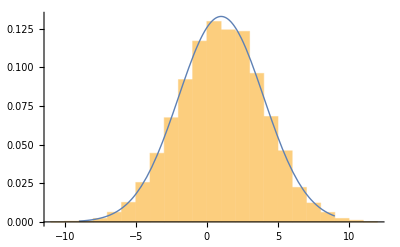

```mathematica
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,-9,9},PlotStyle->Thick]]
```

```mathematica
data=RandomFunction[BernoulliProcess[1/2],{0,100}]
```

TemporalData[…]

```mathematica
ListPlot[data, Joined->True]
```

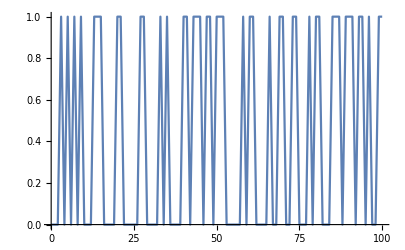

```mathematica
dataP=RandomVariate[PoissonDistribution[2],10^4];
```

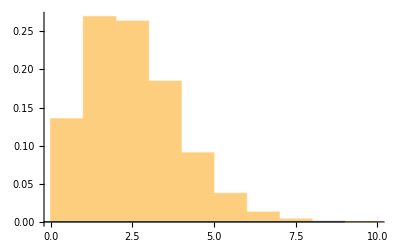

```mathematica
Show[
Histogram[dataP,20,"ProbabilityDensity"],
Plot[PDF[PoissonDistribution[2],x],{x,-9,9},PlotStyle->Thick]]
```

```mathematica
RandomSample[Range[10], RandomInteger[{1, 10}]]
```

{1,5,2,7,6,10,8,3,4,9}

{6,0,2,6,2,2,5,1,3,1,3,6,5,3,2,3,2,4,2,4,2,0,6,4,3,2,4,2,1,4,4,4,1,0,1,5,5,5,2,2,2,1,3,6,3,1,2,2,2,2,3,3,2,2,4,3,6,3,4,3,3,1,4,2,6,4,6,0,1,0,2,2,1,4,2,1,5,3,5,2,3,1,1,3,1,2,6,4,2,0,4,1,0,5,0,6,1,5,4,4,3,2,4,3,1,2,3,0,3,3,5,3,2,2,3,3,7,1,5,2,4,3,4,5,3,4,5,2,4,5,1,5,3,5,2,3,4,3,0,2,5,1,1,2,1,4,4,5,7,6,6,3,3,5,1,1,4,3,2,5,4,4,1,3,0,3,1,0,1,2,2,1,2,1,0,4,2,3,3,2,4,3,2,2,2,3,3,4,4,5,3,2,2,3,4,4,1,3,2,2,5,6,4,5,99592,0,2,4,2,2,2,3,3,5,3,4,4,3,1,5,3,1,8,5,5,3,1,2,3,3,2,3,1,4,3,3,5,3,3,2,4,3,1,4,7,3,7,3,5,3,2,0,6,3,3,2,2,0,5,4,7,0,3,7,0,3,4,4,2,3,2,3,4,4,2,2,3,2,2,3,3,1,2,4,0,2,3,4,6,7,3,8,6,3,3,3,5,3,3,2,4,3,2,5,3,2,5,1,1,1,2,2,3,8,1,4,3,3,4,1,6,2,4,3,3,8,6,5,0,2,1,2,7,1,0,1,3,3,3,5,1,4,5,2,1,4,4,7,0,4,3,2,2,2,0,7,6,4,1,3,1,0,5,1,3,2,3,1,2,1,4,1,2,7,6,1,2,5,3,4,3,2,3,2,3,2,2,4,3,3,1,5,1,4,4,1,1,1,3,5,3,2,5,2,6,3,3,4,6}
 |  |  |  |

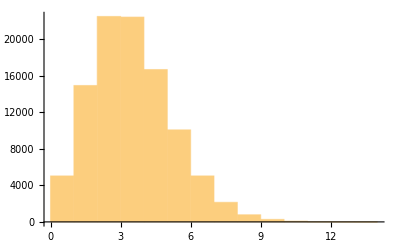

```mathematica
pData=RandomVariate[PoissonDistribution[3],10^5]
Histogram[pData]
```

```mathematica
pData := Count[RandomSample[Range[20], Random[Integer, 10]], _Integer];
```

```mathematica
RandomSample[Range[1000], RandomInteger[5]]
```

{184,406,501}

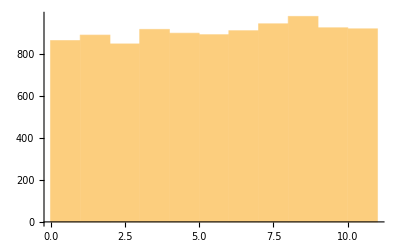

```mathematica
t=Table[pData,10^4];
Histogram[t]
```

```mathematica
prussianHorseKicks= {0,0,0,0,0,0,0,1,1,0,0,0,1,0,2,0,0,0, 0,0,0,0,0,0,0 ,1 ,1,0,3,2,1,1,1,0,0,0,2,1,4,3,0,1,0,0,2,1,0,0,1,0,1,0,0,0,0,1,2,0,0,0,0,1,0,1,1,2,1,4,1,0,0,1,2,0,1,2,1,0,1,0,3,0,0,3,0,1,0,0,0,0,1,0,0,2,0,1,1,0,0,0,0,0,0,1,0,0,2,0,1,0,1,2,1,0,0,1,1,1,0,0,1,0,1,3,0,1,1,2,1,0,0,3,2,1,1,0,1,2,0,0,1,1,0,0,1,1,0,0,0,0,1,1,0,0,0,1,1,0,1,1,0,0,1,2,2,0,2,1,2,0,2,0,1,1,2,0,2,1,1,2,2,0,0,0,1,1,1,0,1,1 ,0,3,3,1,0,1,3,2,0,1,1,3,0,1,1,0,1,1,0,0,1,0,0,0,1,0,2,0,0,1,3, 0,0,1,0,0,0,0,0 ,0,0,1,0,1,1,0,0};
```

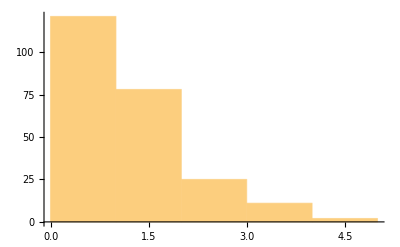

```mathematica
Histogram[prussianHorseKicks]
```

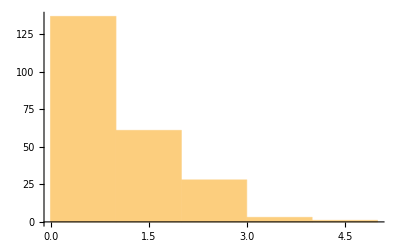

```mathematica
pData=RandomVariate[PoissonDistribution[0.5],230];
Histogram[pData]
```

```mathematica
H = DistributionFitTest[prussianHorseKicks, Automatic, "HypothesisTestData"];
```

```mathematica
H["TestDataTable", All]
```

| Statistic | P-Value
Anderson-Darling | 22.2944 | 0.
Baringhaus-Henze | 1+237/(√(1+(3/2)^(4/5) 79^(2/5)))+2/237 (10619+242 ⅇ^(-(13983 3^(4/5) 79^(2/5))/(2792 2^(4/5)))+1487 ⅇ^(-(125847 3^(4/5) 79^(2/5))/(44672 2^(4/5)))+3933 ⅇ^(-(13983 3^(4/5) 79^(2/5))/(11168 2^(4/5)))+11685 ⅇ^(-(13983 3^(4/5) 79^(2/5))/(44672 2^(4/5))))-1/(√(1+(3^(4/5) 79^(2/5))/(2 2^(4/5))))2 (2 ⅇ^(-35803619/(44672 2^(4/5) 3^(1/5) 79^(3/5) (1+(3^(4/5) 79^(2/5))/(2 2^(4/5)))))+11 ⅇ^(-4333019/(11168 2^(4/5) 3^(1/5) 79^(3/5) (1+(3^(4/5) 79^(2/5))/(2 2^(4/5)))))+25 ⅇ^(-5488475/(44672 2^(4/5) 3^(1/5) 79^(3/5) (1+(3^(4/5) 79^(2/5))/(2 2^(4/5)))))+121 ⅇ^(-1685099/(44672 2^(4/5) 3^(1/5) 79^(3/5) (1+(3^(4/5) 79^(2/5))/(2 2^(4/5)))))+78 ⅇ^(-17051/(2792 2^(4/5) 3^(1/5) 79^(3/5) (1+(3^(4/5) 79^(2/5))/(2 2^(4/5)))))) | 9.48996×10^-10
Cramér-von Mises | 3.80631 | 0.
Jarque-Bera ALM | 82.2385 | 0.
Mardia Combined | 82.2385 | 0.
Mardia Kurtosis | (615645381 √(79/2))/997793792 | 0.000105394
Mardia Skewness | 2849355875200111/44573444276224 | 1.29249×10^-15
Pearson χ^2 | 1397.35 | 6.13846×10^-289
Shapiro-Wilk | 0.758373 | 2.30029×10^-18

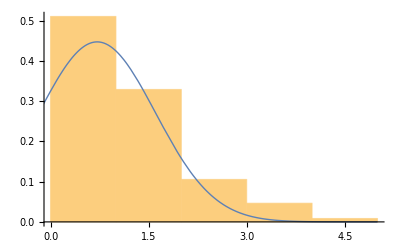

```mathematica
Show[Histogram[prussianHorseKicks,Automatic,"ProbabilityDensity"],Plot[PDF[H["FittedDistribution"],x],{x,-5,5},PlotStyle->Thick]]
```

```mathematica
SetDirectory["C:\\Users\\Kalee\\Documents\\Wolfram Mathematica"]
```

C:\Users\Kalee\Documents\Wolfram Mathematica

```mathematica
test1=Import["data1.txt","Data"]
```

{{1875,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{1876,2,0,0,0,1,0,0,0,0,0,0,0,1,1},{1877,2,0,0,0,0,0,1,1,0,0,1,0,2,0},{1878,1,2,2,1,1,0,0,0,0,0,1,0,1,0},{1879,0,0,0,1,1,2,2,0,1,0,0,2,1,0},{1880,0,3,2,1,1,1,0,0,0,2,1,4,3,0},{1881,1,0,0,2,1,0,0,1,0,1,0,0,0,0},{1882,1,2,0,0,0,0,1,0,1,1,2,1,4,1},{1883,0,0,1,2,0,1,2,1,0,1,0,3,0,0},{1884,3,0,1,0,0,0,0,1,0,0,2,0,1,1},{1885,0,0,0,0,0,0,1,0,0,2,0,1,0,1},{1886,2,1,0,0,1,1,1,0,0,1,0,1,3,0},{1887,1,1,2,1,0,0,3,2,1,1,0,1,2,0},{1888,0,1,1,0,0,1,1,0,0,0,0,1,1,0},{1889,0,0,1,1,0,1,1,0,0,1,2,2,0,2},{1890,1,2,0,2,0,1,1,2,0,2,1,1,2,2},{1891,0,0,0,1,1,1,0,1,1,0,3,3,1,0},{1892,1,3,2,0,1,1,3,0,1,1,0,1,1,0},{1893,0,1,0,0,0,1,0,2,0,0,1,3,0,0},{1894,1,0,0,0,0,0,0,0,1,0,1,1,0,0}}

```mathematica
test2=Rest/@test1
```

{{0,0,0,0,0,0,0,1,1,0,0,0,1,0},{2,0,0,0,1,0,0,0,0,0,0,0,1,1},{2,0,0,0,0,0,1,1,0,0,1,0,2,0},{1,2,2,1,1,0,0,0,0,0,1,0,1,0},{0,0,0,1,1,2,2,0,1,0,0,2,1,0},{0,3,2,1,1,1,0,0,0,2,1,4,3,0},{1,0,0,2,1,0,0,1,0,1,0,0,0,0},{1,2,0,0,0,0,1,0,1,1,2,1,4,1},{0,0,1,2,0,1,2,1,0,1,0,3,0,0},{3,0,1,0,0,0,0,1,0,0,2,0,1,1},{0,0,0,0,0,0,1,0,0,2,0,1,0,1},{2,1,0,0,1,1,1,0,0,1,0,1,3,0},{1,1,2,1,0,0,3,2,1,1,0,1,2,0},{0,1,1,0,0,1,1,0,0,0,0,1,1,0},{0,0,1,1,0,1,1,0,0,1,2,2,0,2},{1,2,0,2,0,1,1,2,0,2,1,1,2,2},{0,0,0,1,1,1,0,1,1,0,3,3,1,0},{1,3,2,0,1,1,3,0,1,1,0,1,1,0},{0,1,0,0,0,1,0,2,0,0,1,3,0,0},{1,0,0,0,0,0,0,0,1,0,1,1,0,0}}

```mathematica
test3=Flatten[test2]
```

{0,0,0,0,0,0,0,1,1,0,0,0,1,0,2,0,0,0,1,0,0,0,0,0,0,0,1,1,2,0,0,0,0,0,1,1,0,0,1,0,2,0,1,2,2,1,1,0,0,0,0,0,1,0,1,0,0,0,0,1,1,2,2,0,1,0,0,2,1,0,0,3,2,1,1,1,0,0,0,2,1,4,3,0,1,0,0,2,1,0,0,1,0,1,0,0,0,0,1,2,0,0,0,0,1,0,1,1,2,1,4,1,0,0,1,2,0,1,2,1,0,1,0,3,0,0,3,0,1,0,0,0,0,1,0,0,2,0,1,1,0,0,0,0,0,0,1,0,0,2,0,1,0,1,2,1,0,0,1,1,1,0,0,1,0,1,3,0,1,1,2,1,0,0,3,2,1,1,0,1,2,0,0,1,1,0,0,1,1,0,0,0,0,1,1,0,0,0,1,1,0,1,1,0,0,1,2,2,0,2,1,2,0,2,0,1,1,2,0,2,1,1,2,2,0,0,0,1,1,1,0,1,1,0,3,3,1,0,1,3,2,0,1,1,3,0,1,1,0,1,1,0,0,1,0,0,0,1,0,2,0,0,1,3,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0}

## Kein’s Junior Breakthrough Challenge Simulations

### Coin Toss Normal Distribution

```mathematica
RandomSample[{0,1}, 1000]
```

RandomSample::smplen: RandomSample cannot generate a sample of length 1000, which is greater than the length of the sample set {0,1}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

```mathematica
RandomChoice[{0,1},1000]
```

{1,1,1,0,0,0,1,1,0,0,1,1,1,1,0,0,0,1,0,1,1,1,1,1,1,0,1,0,1,1,0,0,0,1,1,1,0,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,1,0,0,1,0,0,1,0,0,0,1,1,0,1,0,1,1,0,1,1,1,0,1,1,0,1,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,0,0,1,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,1,0,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,0,1,0,1,0,0,1,1,0,1,0,0,0,1,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,1,1,0,1,0,1,1,1,0,0,1,0,0,0,0,1,0,1,1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,0,0,1,0,0,0,1,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,1,0,0,0,1,1,1,1,0,1,0,1,1,0,0,1,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,1,1,0,1,0,0,0,1,0,0,1,0,0,1,0,0,0,1,0,1,1,0,0,0,0,1,1,1,1,0,0,1,1,1,1,1,0,0,1,1,1,1,1,0,1,0,0,0,0,1,1,1,0,1,1,0,0,1,0,0,0,1,0,0,1,0,1,1,0,1,1,1,1,0,1,0,1,1,0,0,0,0,1,1,0,1,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,0,1,1,0,1,1,1,0,1,0,1,1,0,0,1,1,0,0,0,1,1,0,0,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,1,1,0,0,1,0,1,1,0,0,0,1,1,0,0,0,0,1,0,0,0,1,1,0,1,1,1,0,1,1,0,1,0,0,0,0,1,1,0,0,0,1,0,1,0,0,1,1,0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,1,1,1,1,1,1,1,0,1,0,1,0,0,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,0,1,0,0,1,0,1,0,1,0,1,0,0,1,1,0,1,0,1,1,0,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,0,1,0,0,0,0,0,1,1,0,1,0,0,0,0,1,1,0,1,0,0,1,0,0,0,1,1,1,1,0,1,1,0,1,0,0,0,1,1,0,1,1,0,1,0,1,0,1,0,0,0,1,1,1,1,1,0,0,1,1,1,1,1,0,0,1,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,1,1,1,1,1,1,0,1,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,0,0,1,1,1,0,1,1,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,1,0,1,0,0,0,1,0,1,0,1,1,1,0,0,1,1,1,1,1,1,1,1,0,1,0,1,0,1,0,0,1,1,1,0,0,0,0,1,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,0,1,1,1,0,1,1,1,1,0,0,1,0,0,1,1,1,0,0,1,0,1,1,0,1,0,0,1,0,0,1,0,0,1,1,1,0,1,1,1,0,0,1,1,0,1,1,1,1,1,0,0,1,1,1,0,1,0,0,0,0,1,1,0,1,0,0,1,1,1,0,1,1,0,0,1,1,1,1,0,1,0,0,1,1,0,1,1,1,1,0,1,0,0,1,0,1,0,1,1,1,1,1,0,1,0,1,0,0,1,0,1,0,1}

```mathematica
Count[RandomChoice[{0,1},1000], 0]
```

503

```mathematica
Manipulate[Count[RandomChoice[{0,1},x], 0], {x, 1, 1000, 1}]
```

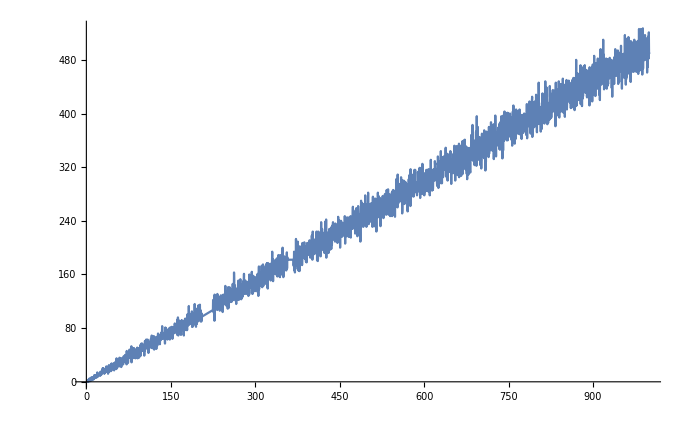

```mathematica
Plot[Count[RandomChoice[{0,1},IntegerPart[x]], 0], {x, 1, 1000}]
```

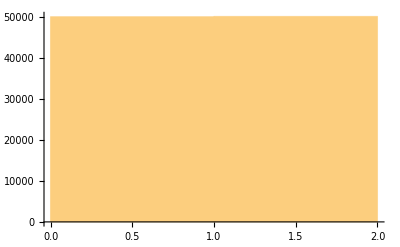

```mathematica
Histogram[RandomChoice[{0,1},100000]]
```

```mathematica
RandomChoice[{0,1},1000]
```

{0,1,1,1,1,1,0,0,1,1,0,0,0,0,1,0,1,1,1,0,1,0,1,1,1,1,0,0,1,1,0,0,1,0,1,0,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1,0,0,0,1,1,1,0,0,0,1,1,1,1,0,1,1,1,1,1,0,1,1,0,0,1,0,1,1,0,0,0,1,0,1,0,0,0,1,1,1,1,1,1,0,0,0,0,1,0,0,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,1,1,1,0,1,0,0,1,1,0,1,0,0,1,1,1,0,1,0,0,1,1,0,1,0,1,1,0,0,0,1,0,1,1,1,0,0,1,0,1,0,1,1,1,0,1,1,1,0,1,0,1,1,0,0,0,1,1,1,1,1,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,1,1,0,1,1,1,1,0,1,1,0,0,1,0,0,0,0,1,1,1,1,0,0,1,1,0,1,0,1,0,0,0,1,0,0,0,1,0,1,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,0,0,0,0,1,1,0,1,1,1,1,0,1,0,1,0,1,1,0,1,0,0,0,1,0,0,0,1,0,1,1,1,0,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,0,1,1,0,0,1,0,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,0,1,1,0,1,1,0,0,1,1,0,1,0,1,1,1,0,0,1,1,1,1,1,0,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,1,0,0,1,1,1,1,1,0,0,1,0,0,1,1,1,1,1,1,0,0,0,1,1,0,1,1,1,1,1,0,0,1,0,0,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,1,1,0,0,0,1,0,0,0,1,0,0,1,1,1,0,0,0,0,1,1,1,1,1,0,0,1,0,1,0,1,1,1,0,1,1,0,0,0,1,0,1,1,0,0,1,0,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,1,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,1,1,1,0,0,1,1,1,0,1,0,1,1,1,1,0,1,1,1,1,0,0,1,0,0,1,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,1,1,1,1,0,1,0,1,1,0,1,0,1,0,1,1,1,0,1,0,1,1,1,0,0,1,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,0,1,1,1,1,1,0,1,1,0,1,0,1,1,1,1,1,1,0,1,0,1,1,0,0,0,1,1,1,1,0,0,1,1,0,0,1,0,1,1,1,1,0,0,0,1,1,0,1,1,0,1,0,0,0,1,0,0,0,0,0,1,1,0,0,0,1,1,1,1,1,1,1,0,0,0,0,1,0,0,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,1,1,0,1,0,1,0,1,1,0,0,0,0,0,0,1,1,0,0,0,1,1,1,0,1,1,0,0,0,1,0,0,1,0,1,0,1,0,0,1,1,1,0,1,0,1,1,0,1,1,1,1,0,1,1,0,1,1,0,0,0,1,1,0,1,1,1,0,1,0,0,0,1,0,0,0,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,1,0,0,0,0,0,1,1,1,1,0,1,0,0,0,0,1,0,0,1,1,1,0,0,0,1,1,1,1,0,0,0,1,0,0,1,1,0,1,1,1,0,1,0,0,1,1,0,1,0,0,1,0,0,0,0,0,1,0,1,1,1,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,1,1,0,1,0,0,1,1,1,1,0,1,0,1,1,0,1,0,0,1,0,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,0,1,1,1,0,0,1,0,0,0,1,1,0,0,1,0,1,1,0,0,1,0,0,1,1,0,0,1,0,1,1,0,0,0}

```mathematica
list = {};
For[i = 0, i<10000, i++, AppendTo[list,Count[RandomChoice[{0,1},1000], 0]]]
```

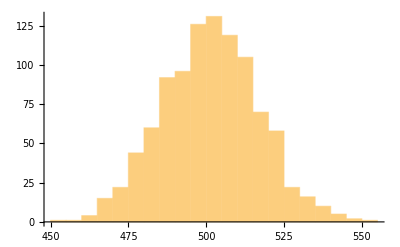

```mathematica
Histogram[list]
```

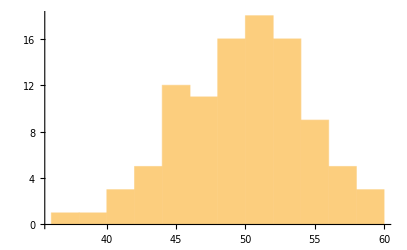

### Functional approach

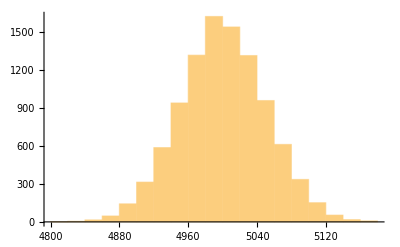

```mathematica
r:=Plus@@RandomChoice[{0,1},10000]
t=Table[r,10^4];
Histogram[t]
```